```mathematica
SetDirectory[NotebookDirectory[]];
Clear["Global`*"];
```

```mathematica
Decreasing of residue(n is number of nodes);
```

```mathematica
(*triangle 1*)
```

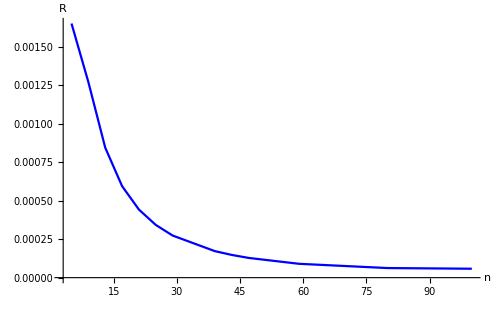

```mathematica
residueT1 = {{5,0.00165247},{9, 0.00127166},{13,0.000845393},{17,0.000595188},{21,0.000442543},{25,0.00034274},{29,0.000273806},{39,0.000172562},{43,0.00014792},{47,0.000128407},{59, 9*10^-5},{80,6.24*10^-5},{100,5.8*10^-5}};
gr1=ListLinePlot[residueT1,
GridLines->Full,
ImageSize->500,
PlotStyle->{Blue},
PlotRange->All,
AxesLabel->{Style["n",16,Black,Italic,FontFamily->"Times"],Style["R",16,Italic,Black,FontFamily->"Times"]},
AxesStyle->Directive[Black,14,FontFamily->"Times"],
AxesStyle->Thick,Axes->True]
```

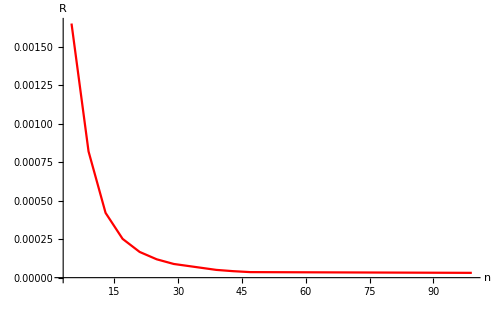

```mathematica
(*triangle 2*)
residueT2= {{5,0.00165258},{9, 0.000820719},{13,0.000421139},{17,0.00025212},{21,0.000167229},{25,0.00011939},{29,8.90327*10^-5},{39,5.04366*10^-5},{43,4.20686*10^-5},{47,3.60014*10^-5},{99,3.12022*10^-5 }};
gr2=ListLinePlot[residueT2,
GridLines->Full,
ImageSize->500,
PlotStyle->{Red},
PlotRange->All,
AxesLabel->{Style["n",16,Black,Italic,FontFamily->"Times"],Style["R",16,Italic,Black,FontFamily->"Times"]},
AxesStyle->Directive[Black,14,FontFamily->"Times"],
AxesStyle->Thick,Axes->True]
```

```mathematica
(*rectangle 1*)
```

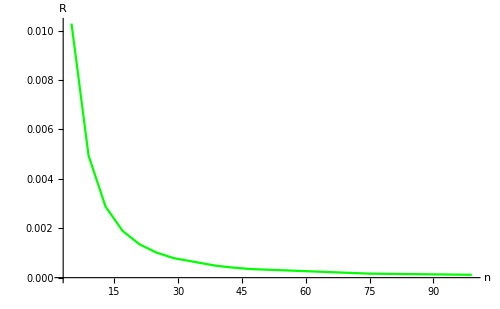

```mathematica
residueR1 = {{5,0.0102857},{9, 0.004942},{13,0.00287331},{17,0.00189056},{21,0.00134604},{25,0.00101159},{29,0.000790502},{39,0.000479795},{43,0.000406233},{47,0.000348887},{75,0.000162506},{99,0.000115556}};
gr3=ListLinePlot[residueR1,
GridLines->Full,
ImageSize->500,
PlotStyle->{Green},
PlotRange->All,
AxesLabel->{Style["n",16,Black,Italic,FontFamily->"Times"],Style["R",16,Italic,Black,FontFamily->"Times"]},
AxesStyle->Directive[Black,14,FontFamily->"Times"],
AxesStyle->Thick,Axes->True]
```

```mathematica
(*rectangle 2*)
```

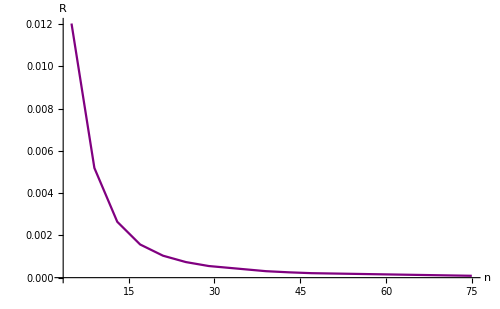

```mathematica
residueR2= {{5,0.012035},{9, 0.00519328},{13,0.00264602},{17,0.00157127},{21,0.00103941},{25,0.000737648},{29,0.000550401},{39,0.000306306},{43,0.00025253},{47,0.000211985},{75,8.79122*10^-5}};
gr4=ListLinePlot[residueR2,
GridLines->Full,
ImageSize->500,
PlotStyle->{Purple},
PlotRange->All,
AxesLabel->{Style["n",16,Black,Italic,FontFamily->"Times"],Style["R",16,Italic,Black,FontFamily->"Times"]},
AxesStyle->Directive[Black,14,FontFamily->"Times"],
AxesStyle->Thick,Axes->True]
```

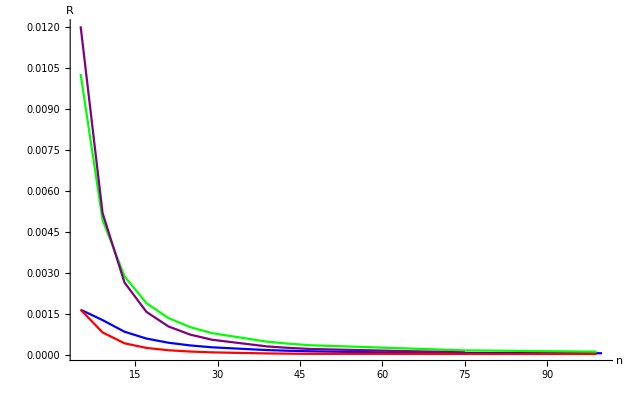

```mathematica
Show[gr1,gr2,gr3,gr4,PlotRange->All]
```

```mathematica
Decreasing of residue(n is number of finite elements);
```

```mathematica
Print["Triangles 1",Solve[(n-1)(n-1)*2==18.0,n]]
Print["Triangles 2",Solve[(n-1)/2(n-1)/2*2==18.0,n]]
Print["Rectangles 1",Solve[(n-1)(n-1)==16.0,n]]
Print["Rectangles 2",Solve[(n-1)/2(n-1)/2==16.0,n]]
```

Triangles 1{{n→-2.},{n→4.}}

Triangles 2{{n→-5.},{n→7.}}

Rectangles 1{{n→-3.},{n→5.}}

Rectangles 2{{n→-7.},{n→9.}}